# Project 1 - IX1501

## A project by William Lewin & Elias Chahine

wlewin@kth.se & echahine@kth.se

## Summary

In the discrete math course you learned how to do a census by computing all possibilities and use the classical definition of probability. In the following problems you are expected to use convolution.
-Graphics-
At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 

At a fun-fair stall you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact probability function of the sum.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Determine the expected investment to win a Teddy.

What’s the probability of winning (at least one) Teddy if you play twenty times?

## Mathematic formulas & equations

### Determine the exact probability function of the sum.

### Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

### Determine the expected investment to win a Teddy.

### What’s the probability of winning (at least one) Teddy if you play twenty times?

## Discussion

## Code

4

6

8

12

20

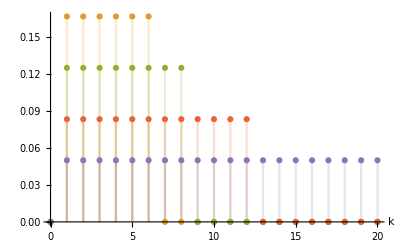

```mathematica
ClearAll["Global`*"]
pyramid = PolyhedronData["TriangularPyramid","FaceCount"]
cube = PolyhedronData["Cube","FaceCount"]
octahedron = PolyhedronData["Octahedron","FaceCount"]
dodecahedron = PolyhedronData["Dodecahedron","FaceCount"]
icosahedron = PolyhedronData["Icosahedron","FaceCount"]




(*Random throws*)
d1 := RandomInteger[{1,pyramid}]
d2 := RandomInteger[{1,cube}]
d3 := RandomInteger[{1,octahedron}]
d4 := RandomInteger[{1,dodecahedron}]
d5 := RandomInteger[{1,icosahedron}]
```

```mathematica
(*Prob. P1 ≤ 10 och P2 ≥ 45
convolutePyramidCube
convolutePCOctagon
convolutePCODodecahedron
convolutePCODIco....
*)
ClearAll["`*"]
pyramidfX[k_]=Piecewise[{{1/4,1≤k≤4}}];
cubefX[k_]=Piecewise[{{1/6,1≤k≤6}}];
octafX[k_]:=Piecewise[{{1/8,1≤k≤8}}];
dodefX[k_]:=Piecewise[{{1/12,1≤k≤12}}];
icofX[k_]:=Piecewise[{{1/20,1≤k≤20}}];
DiscretePlot[{pyramidfX[y],cubefX[k],octafX[k],dodefX[k],icofX[k]},{k,0,20},AxesLabel->Automatic]
```

-Graphics-

```mathematica
convolutePyramidCube[k_]:=Convolve[pyramidfX[x],cubefX[x],x,y]; 
convolutePCOctagon[k_]:=Convolve[convolutePyramidCube[x],octafX[x],x,y];
convolutePCODodecahedron[k_]:= Convolve[convolutePCOctagon[x],dodefX[x],x,y];
convolutePCODIcosahedron[k_]:=Convolve[convolutePCODodecahedron[x],icofX[x],x,y];
convPCODI[k_]:=convolutePCODIcosahedron[x];(*One big piecewise function*)
```

```mathematica
convPCODI[x]
```

Piecewise[{{1463/15360, 5<y≤7}, {-(1463 (-10+y))/46080, 7<y<10}, {(1463 (-2+y))/46080, 2<y≤5}, {0, True}}]

```mathematica
DiscretePlot[convPCODI[k],{k,2,10},AxesLabel->Automatic]
```

-Graphics-

```mathematica
f1[x_]:= 1+x;
f2[x_]:= x^2;
```

```mathematica
Convolve[f1[x],f2[y],x,y]
```

Convolve[1,y^2,x,y]+Convolve[x,y^2,x,y]